```mathematica
Series[Log[Tanh[k]],{k,Infinity,1}]
```

Log[Tanh[k]]

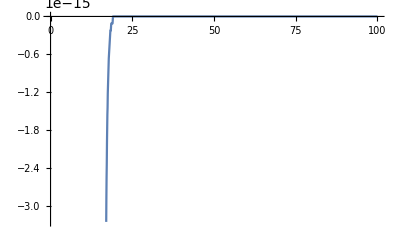

```mathematica
Plot[%,{k,0,100}]
```

```mathematica
?ContourPlot
```

ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a contour plot of f as a function of x and y. 
ContourPlot[f==g,{x,x_min,x_max},{y,y_min,y_max}] plots contour lines for which f=g. 
ContourPlot[{f_1==g_1,f_2==g_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several contour lines.

```mathematica
?Series
```

Series[f,{x,x_0,n}] generates a power series expansion for f about the point x=x_0 to order (x-x_0)^n. 
Series[f,{x,x_0,n_x},{y,y_0,n_y},…] successively finds series expansions with respect to x, then y, etc.

```mathematica
a=z+n
```

n+z

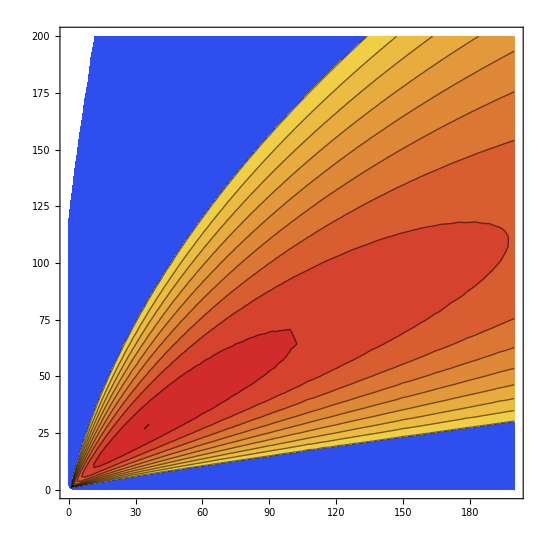

```mathematica
ContourPlot[-(-15.4a+16.9a^(2/3)+0.7z^2/a^(1/3)+22.4(n-z)^2/a)/a,{n,0,200},{z,0,200},Contours->Range[0,12]~Join~{8.685},ColorFunction->"TemperatureMap"]
```

```mathematica
?ContourPlot
```

ContourPlot[f,{x,x_min,x_max},{y,y_min,y_max}] generates a contour plot of f as a function of x and y. 
ContourPlot[f==g,{x,x_min,x_max},{y,y_min,y_max}] plots contour lines for which f=g. 
ContourPlot[{f_1==g_1,f_2==g_2,…},{x,x_min,x_max},{y,y_min,y_max}] plots several contour lines.

```mathematica
Solve[D[-(-15.4a+16.9a^(2/3)+0.7z^2/a^(1/3)+22.4(n-z)^2/a)/a,z]==0,n]
```

$Aborted

$Aborted

```mathematica
D[-(-15.4a+16.9a^(2/3)+0.7z^2/a^(1/3)+22.4(n-z)^2/a)/a,z]
```

(15.4+(22.4 (n-z)^2)/(n+z)^2+(0.233333 z^2)/(n+z)^(4/3)+(44.8 (n-z))/(n+z)-11.2667/(n+z)^(1/3)-(1.4 z)/(n+z)^(1/3))/(n+z)-(-(22.4 (n-z)^2)/(n+z)-(0.7 z^2)/(n+z)^(1/3)-16.9 (n+z)^(2/3)+15.4 (n+z))/(n+z)^2

```mathematica
FullSimplify[%]
```

1/(n+z)^(13/3)(n^2 (16.9-3.26667 z) z+n z^2 (16.9-2.33333 z-89.6 (n+z)^(1/3))+z^3 (5.63333-0.466667 z-1.77636×10^-15 (n+z)^(1/3))+n^3 (5.63333-1.4 z+89.6 (n+z)^(1/3)))

```mathematica
Solve[1/(n+z)^(13/3)(n^2 (16.899999999999995-3.2666666666666666 z) z+n z^2 (16.9-2.3333333333333335 z-89.6 (n+z)^(1/3))+z^3 (5.633333333333334-0.4666666666666666 z-1.776356839400251*^-15 (n+z)^(1/3))+n^3 (5.633333333333334-1.4 z+89.6 (n+z)^(1/3)))==0,z]
```

$Aborted

```mathematica
Table[NSolve[n>=0&&n<300&&1/(n+z)^(13/3)(n^2 (16.899999999999995-3.2666666666666666 z) z+n z^2 (16.9-2.3333333333333335 z-89.6 (n+z)^(1/3))+z^3 (5.633333333333334-0.4666666666666666 z-1.776356839400251*^-15 (n+z)^(1/3))+n^3 (5.633333333333334-1.4 z+89.6 (n+z)^(1/3)))==0,n,Reals][[1,1,2]],{z,1,118}]
```

{0.825064,1.78026,2.78442,3.82527,4.89696,5.99599,7.11996,8.26713,9.43614,10.6259,11.8356,13.0645,14.3118,15.5772,16.86,18.1599,19.4765,20.8094,22.1584,23.5231,24.9033,26.2989,27.7094,29.1348,30.5749,32.0295,33.4984,34.9814,36.4786,37.9896,39.5144,41.0528,42.6048,44.1702,45.749,47.341,48.9462,50.5644,52.1956,53.8397,55.4967,57.1664,58.8488,60.5438,62.2514,63.9715,65.7041,67.449,69.2063,70.9759,72.7577,74.5518,76.3579,78.1762,80.0066,81.849,83.7033,85.5697,87.4479,89.3381,91.24,93.1538,95.0794,97.0168,98.9659,100.927,102.899,104.883,106.879,108.886,110.905,112.936,114.978,117.031,119.096,121.173,123.261,125.36,127.471,129.594,131.727,133.872,136.029,138.197,140.376,142.566,144.768,146.981,149.205,151.441,153.688,155.946,158.215,160.496,162.788,165.091,167.405,169.73,172.067,174.415,176.774,179.144,181.525,183.918,186.322,188.737,191.162,193.6,196.048,198.507,200.978,203.459,205.952,208.456,210.971,213.497,216.034,218.583}

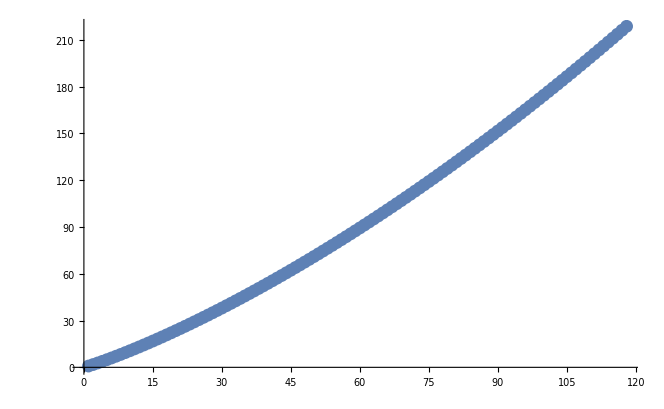

```mathematica
ListPlot[%]
```

```mathematica
%50[[92]]+92
```

247.946